## Introductions

Hückel molecular orbital theory describes the pi electrons in planar molecules.  For background theory, see Schrier, Introduction to Computational Physical Chemistry (University Science Books, 2017), Chapter 6.  A preview version of this chapter is available at the publisher’s website  http://www.uscibooks.com/schrier.htm

The code in this package largely follows the approach described in that chapter.  However, as the book is meant to be pedagogical for students who are new to programming and easily implemented in different programming languages, it does not take full advantage of the functional programing paradigm in Mathematica.  In contrast, this package does.  This package also makes extensive use of the Molecule[] functionality that was released in Mathematica 12 (2019).

## Functions provided

Numerical calculation.  All functions take a Molecule[] as an input.  Outputs are in units of the C-C coupling index, t.

HuckelHamiltonianMatrix

HuckelMO

HuckelChargeDensityMatrix

Plotting functionality.  Again, all functions take a Molecule[] as input and return plots of the relevant quantity on the atoms.  The plots have tooltips which give the precise numerical values.

HuckelMOPlot

HuckelBondOrderPlot

HuckelTotalElectronsPlot

HuckelNetChargePlot

### Setup

Note:  To install Packages in Mathematica, go to File >> Install...

```mathematica
<<HuckelTheory` (*load the package*)
m=Molecule["hexatriene"] (*create an example molecule*)
Molecule[…]
```

Molecule[…]

Molecule[…]

### Hamiltonian construction

```mathematica
?HuckelHamiltonianMatrix
```

```mathematica
HuckelHamiltonianMatrix[m]//MatrixForm
```

(0 | -1. | 0 | 0 | 0 | 0
-1. | 0 | -1. | 0 | 0 | 0
0 | -1. | 0 | -1. | 0 | 0
0 | 0 | -1. | 0 | -1. | 0
0 | 0 | 0 | -1. | 0 | -1.
0 | 0 | 0 | 0 | -1. | 0)

### Molecular orbital calculations

#### HuckelMO

```mathematica
?HuckelMO
```

```mathematica
HuckelMO[m]
```

<|-1.80194→{0.231921,0.417907,0.521121,0.521121,0.417907,0.231921},-1.24698→{-0.417907,-0.521121,-0.231921,0.231921,0.521121,0.417907},-0.445042→{-0.521121,-0.231921,0.417907,0.417907,-0.231921,-0.521121},0.445042→{-0.521121,0.231921,0.417907,-0.417907,-0.231921,0.521121},1.24698→{-0.417907,0.521121,-0.231921,-0.231921,0.521121,-0.417907},1.80194→{-0.231921,0.417907,-0.521121,0.521121,-0.417907,0.231921}|>

#### HuckelMOPlot

```mathematica
?HuckelMOPlot
```

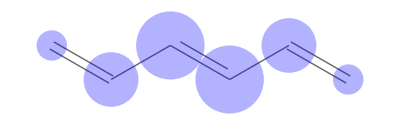
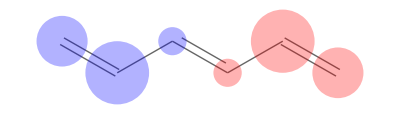
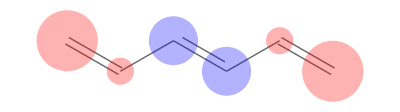
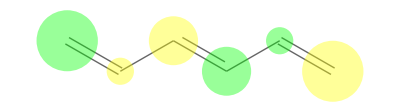
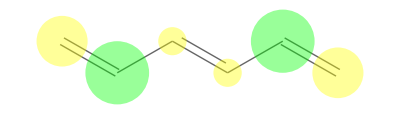
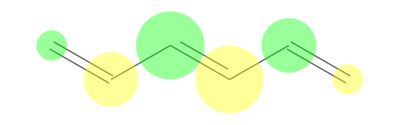
<|-1.80194→-Graphics-,-1.24698→-Graphics-,-0.445042→-Graphics-,0.445042→-Graphics-,1.24698→-Graphics-,1.80194→-Graphics-|>

```mathematica
HuckelMOPlot[m]
```

### Bond order and charge

#### HuckelChargeDensityMatrix

```mathematica
?HuckelChargeDensityMatrix
```

```mathematica
HuckelChargeDensityMatrix[m]//MatrixForm
```

(1. | 0.871119 | 0 | -0.387685 | 0 | 0.301417
0.871119 | 1. | 0.483435 | 0 | -0.0862679 | 0
0 | 0.483435 | 1. | 0.784851 | 0 | -0.387685
-0.387685 | 0 | 0.784851 | 1. | 0.483435 | 0
0 | -0.0862679 | 0 | 0.483435 | 1. | 0.871119
0.301417 | 0 | -0.387685 | 0 | 0.871119 | 1.)

#### HuckelBondOrderPlot

```mathematica
?HuckelBondOrderPlot
```

```mathematica
HuckelBondOrderPlot[m]
```

-Graphics-

#### HuckelTotalElectronsPlot

```mathematica
?HuckelTotalElectronsPlot
```

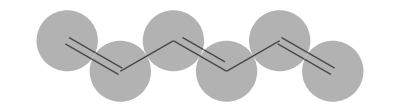

```mathematica
HuckelTotalElectronsPlot[m]
```

#### HuckelNetChargePlot

```mathematica
?HuckelNetChargePlot
```

This is rather boring for alternant hydrocarbons, like hexatriene (where the net pi-charge is zero on each atom)

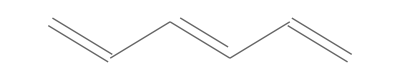

```mathematica
HuckelNetChargePlot[m]
```

It is much more interesting for something like Azulene

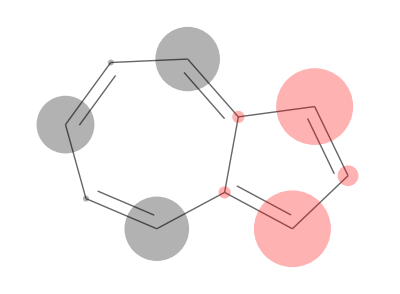

```mathematica
HuckelNetChargePlot[Molecule["azulene"]]
```

## Scope and generalizability

The HuckelTheory package is general enough to treat most heteroaromatic systems (B, N, O, F, Cl, Br), using the Streitwieser parameters. (See Intro to Computational Physical Chemistry, Table 6.1, p. 154).

Atoms considered part of the pi system are:

Any sp2 atom

oxygens, nitrogens, and halogens connected to the pi system

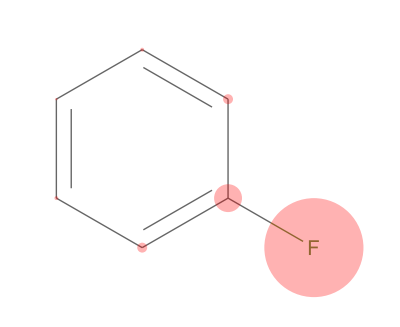
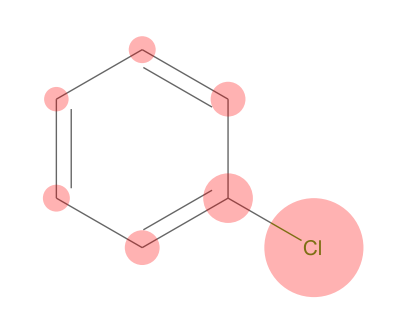
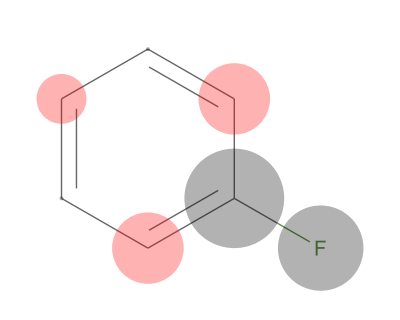
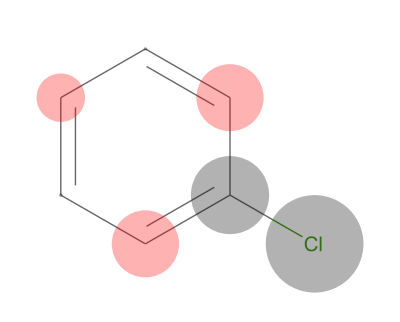
| O | F | Cl | Br
Lowest Energy π-MO | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Lowest eigenvalue | -2.4622 | -3.19718 | -2.20046 | -2.03074
Net Charge | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bond Orders | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
o = Molecule["phenol"];
f=Molecule["fluorobenzene"];
br=Molecule["bromobenzene"];
cl=Molecule["chlorobenzene"];

TableForm[
{First@HuckelMOPlot[#],First@Keys@HuckelMOPlot[#],HuckelNetChargePlot[#],HuckelBondOrderPlot[#]}&/@{o,f,cl,br}//Transpose,
TableHeadings->{{"Lowest Energy π-MO","Lowest eigenvalue","Net Charge","Bond Orders"},{"O","F","Cl","Br"}}
]
```

## Potential limitations

Charge-density based calculations (bond orders, net charges, etc.) depend on having an even number of pi-electrons.

## Other neat examples

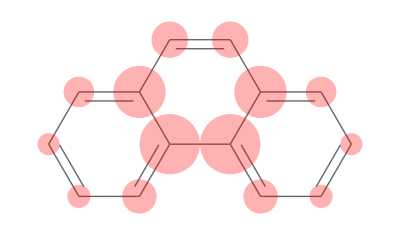
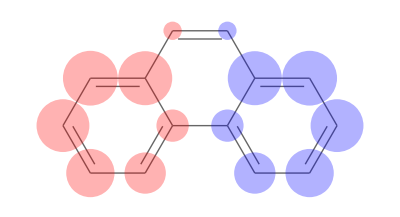
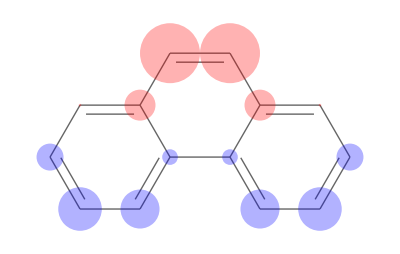
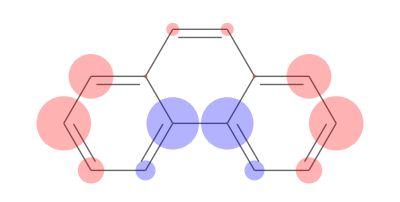
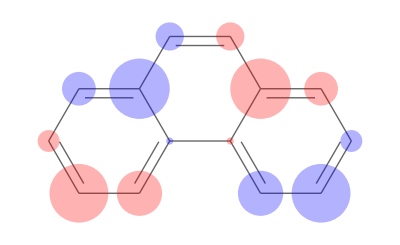
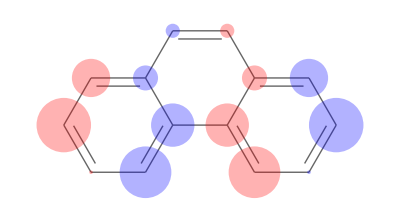
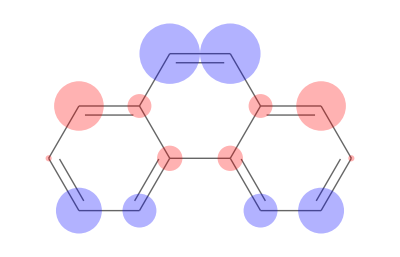
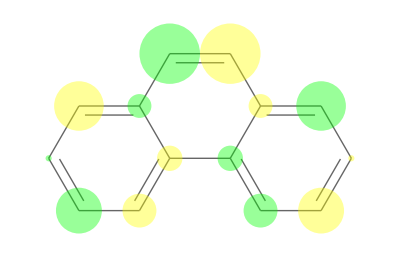
<|-2.43476→-Graphics-,-1.95063→-Graphics-,-1.51627→-Graphics-,-1.3058→-Graphics-,-1.14238→-Graphics-,-0.769052→-Graphics-,-0.605225→-Graphics-,0.605225→-Graphics-,0.769052→-Graphics-,1.14238→-Graphics-,1.3058→-Graphics-,1.51627→-Graphics-,1.95063→-Graphics-,2.43476→-Graphics-|>

```mathematica
HuckelMOPlot@Molecule["phenanthrene"]
```